### dopplerC_estimate.nb Estimate Doppler parameters Carl Tape and Bella Seppi October 20, 2025

```mathematica
ClearParms
```

### Solve for v in terms of Frange

```mathematica
FullSimplify[Solve[FR==(2 c v fs)/(c^2-v^2),v]]
```

{{v→-(c fs+√(c^2 (FR^2+fs^2)))/FR},{v→(-c fs+√(c^2 (FR^2+fs^2)))/FR}}

## Example Doppler curve

```mathematica
SetParms
```

```mathematica
fs
t0
Ft[v,t0,d0,fs,c,t0]
tp0
Ft[v,t0,d0,fs,c,tp0]
```

110.

215.

112.388

217.915

110.

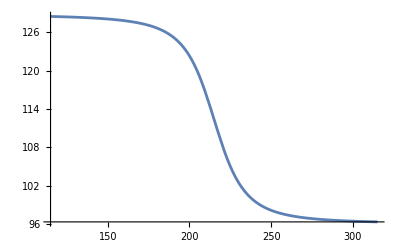

```mathematica
Plot[Ft[v,t0,d0,fs,c,tp],{tp,t0-100,t0+100}]
```

### Note: the roots of the third derivative give time values at the inflection points.

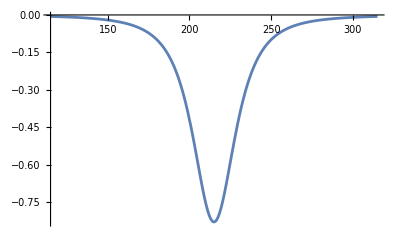

```mathematica
Plot[D1F[v,t0,d0,fs,c,tp],{tp,t0-100,t0+100},PlotRange->All]
```

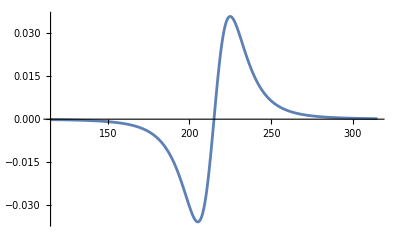

```mathematica
Plot[D2F[v,t0,d0,fs,c,tp],{tp,t0-100,t0+100},PlotRange->All]
```

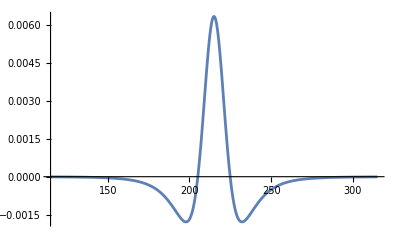

```mathematica
Plot[D3F[v,t0,d0,fs,c,tp],{tp,t0-100,t0+100},PlotRange->All]
```

## Estimating a Doppler curve from data The X tags denote measured variables (different from true values).

### 1. Assume you know c, but maybe you’re off by a bit.

```mathematica
cX=0.9c;
```

### 2. Calculate Fapproach and Frecede.

```mathematica
FapproachX=132.;
FrecedeX=100.;
FrangeX=FapproachX-FrecedeX;
FmeanX=(FrecedeX+FapproachX)/2
```

116.

### 3. Calculate approximation to fs, then use it to get an approximate t0. (So we pick the intersection of the horizontal line FtX with the true spectrum.)

```mathematica
FratioX=0.95;     (* shift factor is a function of v and c only *)
```

```mathematica
fsX=FratioX FmeanX
```

110.2

```mathematica
t0X=First[tp/. NSolve[Ft[v,t0,d0,fs,c,tp]==fsX,tp]]
```

217.667

```mathematica
fs
tp0
```

110.

217.915

### 4. Calculate v using the equation at the top.

```mathematica
vX=(-cX fsX+cX √(fsX^2+ FrangeX^2))/FrangeX
```

43.9134

### We now have curves with only two unknowns: tp and d0. See details in dopplerB_forward.nb

```mathematica
Clear[d0]
```

```mathematica
Fvaryd0[d0_,tp_]:=Ft[v,t0,d0,fs,c,tp]
Fvaryd0est[d0_,tp_]:=Ft[vX,t0X,d0,fsX,cX,tp]
```

```mathematica
Fvaryd0[d0,tp]
Fvaryd0est[d0,tp]
```

110./(1+(7.44687 (-215.-0.00291545 d0 √(0.97875+(2500 (-215.+tp)^2)/d0^2)+tp))/(√(d0^2+2609.73 (-215.-0.00291545 d0 √(0.97875+(2500 (-215.+tp)^2)/d0^2)+tp)^2)))

110.2/(1+(6.3758 (-217.667-0.00323939 d0 √(0.979764+(1928.38 (-217.667+tp)^2)/d0^2)+tp))/(√(d0^2+2008.86 (-217.667-0.00323939 d0 √(0.979764+(1928.38 (-217.667+tp)^2)/d0^2)+tp)^2)))

### 5. Calculate d0 from the slope of the Doppler at (t0p, fs).

### F[ tp ] at tp = t0 and tp = tp0

```mathematica
FullSimplify[Ft[v,t0,d0,fs,c,t0]]
FullSimplify[Ft[v,t0,d0,fs,c,t0],Assumptions->{d0>0}]
FullSimplify[Ft[v,t0,d0,fs,c,t0+d0/c]]
```

110.05+(2.33852 d0)/(√(d0^2))

112.388

110.

### Compare the two Doppler curves

```mathematica
SetParms
```

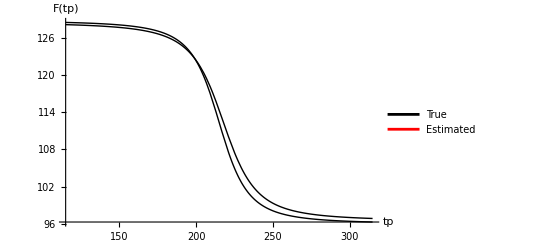

```mathematica
Plot[{
Style[Ft[v,t0,d0,fs,c,tp],Black],
Style[Ft[vX,t0X,d0,fsX,cX,tp],Red]},{tp,t0-100,t0+100},PlotLegends->{"True","Estimated"},AxesLabel->{"tp","F(tp)"},PlotRange->All]
```

### Plot the slope (here we assume that d0 is known). (Notice whether the curves are offset in time from each other.)

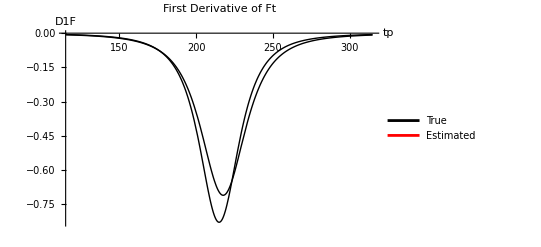

```mathematica
Plot[{
Style[D1F[v,t0,d0,fs,c,tp],Black],
Style[D1F[vX,t0X,d0,fsX,cX,tp],Red]},{tp,t0-100,t0+100},PlotLegends->{"True","Estimated"},PlotLabel->"First Derivative of Ft",AxesLabel->{"tp","D1F"},PlotRange->All]
```

### Measure the maximal slope by choosing two points, then solve for d0. check that the “full simplify” expression reduces to the D1Ft0 expression:

```mathematica
Clear[d0]
```

```mathematica
D1Ft0[vX,d0,fsX,cX]
FullSimplify[D1F[vX,t0X,d0,fsX,cX,t0X],Assumptions->d0>0]
```

-709.832/d0

-709.832/d0

### solve for d0:

```mathematica
xslope =-0.8;
d0X=d0factort0[vX,fsX,cX]/xslope
```

887.29

### a numerical solve will produce + and - values:

```mathematica
Solve[D1F[vX,t0X,d0z,fsX,cX,t0X]==xslope,d0z]
```

{{d0z→-818.291},{d0z→887.29}}

### These values are different if you use the measured slope and the true spectrum:

```mathematica
SetParms
Solve[D1F[v,t0,d0z,fs,c,t0]==xslope,d0z]
d0factort0[v,fs,c]/xslope
d0
```

{{d0z→-950.65},{d0z→1035.}}

1035.

1000.

### we can now compare the arrival times

```mathematica
tp0
tp0X=t0X-d0X/cX
```

217.915

214.792

## Alternatively you could measure the slope at t = t0p

### Note: The slope at tp = t0 is steeper than the slope at tp = tp0.

```mathematica
Clear[d0]
```

```mathematica
D1Ftp0[v,d0,fs,c]
D1Ft0[v,d0,fs,c]
```

-801.749/d0

-828.001/d0

### check that the “full simplify” expression reduces to the very clean version in D1Ftp0:

```mathematica
D1Ftp0[vX,d0,fsX,cX]
FullSimplify[D1F[vX,t0X,d0,fsX,cX,t0X+d0/cX],Assumptions->d0>0]
```

-688.396/d0

-688.396/d0

### solve for d0:

```mathematica
xslope =-0.8;
d0X=d0factortp0[vX,fsX,cX]/xslope
```

860.495

### a numerical solve will produce + and - values:

```mathematica
Solve[D1F[vX,t0X,d0z,fsX,cX,t0X+d0z/cX]==xslope,d0z]
```

{{d0z→-860.495},{d0z→860.495}}

### we can now compare the arrival times

```mathematica
tp0
tp0X=t0X-d0X/cX
```

217.915

214.879